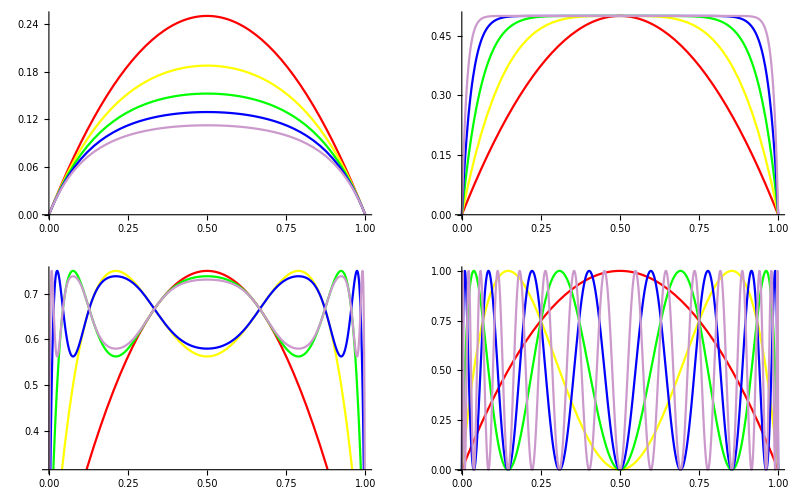

```mathematica
(* General logistic mapping plots in table form *)
recurrenceList[r_,x0_,n_:50]:=NestList[(r # (1-#))&,x0,n-1]

Module[{fns,colors},colors={Red,Yellow,Green,Blue,Lighter[Purple,0.6]};
GraphicsGrid@Partition[Table[fns=Table[recurrenceList[r,x][[n+1]],{n,1,5}];
Plot[fns,{x,0,1},PlotStyle->colors],{r,1,4}],2]]
```

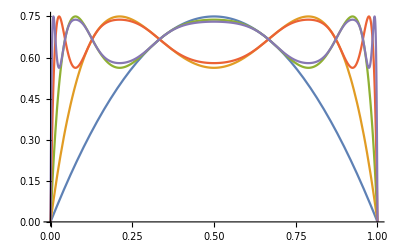

```mathematica
(* General logistic mapping plots in single graph form *)
funcs=RecurrenceTable[{x[n+1]==r x[n] (1-x[n]),x[0]==x0},x,{n,1,5}];
Plot[funcs/. r->3,{x0,0,1},Evaluated->True,PlotRange->All]
```

```mathematica
(* General logistic mapping plots in interactive graph form *)
funcs=RecurrenceTable[{x[n+1]==r x[n] (1-x[n]),x[0]==x0},x,{n,1,5}];
Manipulate[Plot[funcs/. r->rr,{x0,0,1},Evaluated->True,PlotRange->All,ImageSize->500,PlotLabel->Row[{"r = ",rr}],LabelStyle->18],{rr,-2,4,.01}]
```